# Complex Velocity Potential

An analytic function f(z)=ϕ(x,y)+ⅈ ψ(x,y) gives a fluid velocity field
	f'(z)=u(x,y)-ⅈ v(x,y)
satisfying the incompressibility equation
	∂_x u+∂_y v=0
and the irrotational equation
	∂_x v-∂_y u=0.
If you have never seen the 2D curl is is just the third component of the 3D curl of “2D” velocity field 	
	{u(x,y),v(x,y),0}

```mathematica
Curl[{u[x,y],v[x,y],0},{x,y,z}]
```

{0,0,-u^(0,1)[x,y]+v^(1,0)[x,y]}

The point is that the velocity potential ϕ and the stream function ψ  are automatic given any analytic function.  This is like finding a huge library of 2D flows.  Some of those flows were useful in the relatively early development of flight. We do need to be careful about the minis sign on the y-component of the velocity.

## Divergence: Def and pictures.

```mathematica
Clear[xMin,xMax,yMin,yMax,vel,x,y,div]
{{xMin,xMax},{yMin,yMax}}={{-4,4},{-3,3}};
vel[{x_,y_}]:= {Sin[x +y], Cos[x-y^2]}
div[{x_,y_}]=D[vel[{x,y}]⟦1⟧,x]+D[vel[{x,y}]⟦2⟧,y];
TabView[{
"vel"->(streamPic=StreamPlot[vel[{x,y}],{x,xMin,xMax},{y,yMin,yMax}]),
"div"->(divPic=ContourPlot[div[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic]),
"vel & div" ->Show[divPic,streamPic]
},3]
```

123

## 2D Curl: Def and pictures.

```mathematica
Clear[xMin,xMax,yMin,yMax,vel,x,y,curl]
{{xMin,xMax},{yMin,yMax}}={{-4,4},{-3,3}};
vel[{x_,y_}]:= {y ArcTan[x ], Cos[Sin[x-y^2]]}
curl[{x_,y_}]=D[vel[{x,y}]⟦2⟧,x]-D[vel[{x,y}]⟦1⟧,y];
TabView[{
"vel"->(streamPic=StreamPlot[vel[{x,y}],{x,xMin,xMax},{y,yMin,yMax}]),
"curl"->(curlPic=ContourPlot[curl[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic]),
"vel & curl" ->Show[curlPic,streamPic]
},3]
```

123

It might help visualization to have a draggable 2D square and/or circle to see circulation and accumulation.  A drop down with some sample functions would be useful with a “pop-up” entry box. Are the colors OK?

```mathematica
(*Define Dimensions*)
hubRadius=0.2;
(*The size of the center cylinder*)
hubThickness=0.4;(*How thick the center hub is*)
bladeLength=0.8;(*How far each blade sticks out from the hub*)
bladeWidth=0.4;
(*The height/width of the flat blade face*)
bladeThickness=0.05;(*The thickness of the blade material*)
numBlades=5;(*Total number of blades*)
(*Generate the 3D Model*)
Graphics3D[{
(*Center Hub*)
EdgeForm[Red],{Gray,Cylinder[{{0,0,-hubThickness/2},{0,0,hubThickness/2}},hubRadius]},
(*Individual Blades*){LightGray,Table[Rotate[Cuboid[{hubRadius,-bladeThickness/2,-bladeWidth/2},{hubRadius+bladeLength,bladeThickness/2,bladeWidth/2}],a,{0,0,1},{0,0,0}],{a,0,2 Pi-(2 Pi/numBlades),2 Pi/numBlades}]}},Boxed->True,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
paddleWheel=Graphics3D[{(*Axle*)Gray,Cylinder[{{0,0,-0.5},{0,0,0.5}},0.1],(*Hub*)Darker[Gray],Cylinder[{{0,0,-0.1},{0,0,0.1}},0.3],(*Blades*)Table[{LightBlue,Rotate[Cuboid[{-0.05,0.3,-0.4},{0.05,1.2,0.4}],i*2 Pi/6,{0,0,1}]},{i,0,5}]},Boxed->False,Lighting->"Neutral"]
```

-Graphics3D-

## 2D Curl and Div: Pictures.

```mathematica
Clear[xMin,xMax,yMin,yMax,vel,x,y,div,curl]
{{xMin,xMax},{yMin,yMax}}={{-4,4},{-3,3}};
vel[{x_,y_}]:= {Sin[x +y], Cos[x-y^2]}
div[{x_,y_}]=D[vel[{x,y}]⟦1⟧,x]+D[vel[{x,y}]⟦2⟧,y];
curl[{x_,y_}]=D[vel[{x,y}]⟦2⟧,x]-D[vel[{x,y}]⟦1⟧,y];
TabView[{
"vel"->(streamPic=StreamPlot[vel[{x,y}],{x,xMin,xMax},{y,yMin,yMax}]),
"div"->(curlPic=ContourPlot[div[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic]),
"curl"->(curlPic=ContourPlot[curl[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic]),
"vel & div" ->Show[divPic,streamPic],
"vel & curl" ->Show[curlPic,streamPic]
},4]
```

12345

## Complex Velocity Potential and Streamlines f(z)=ϕ(x,y)+ⅈ ψ(x,y)

```mathematica
{{xMin,xMax},{yMin,yMax}}={{-1,1},{-1,1}};
f[z_]:= (1.2+ⅈ)+Sin[(3.2 -2 ⅈ)z]
vel[{x_,y_}]:=ReIm[f'[x+ⅈ y]]*{1,-1}
TabView[{
"flow"->(flowPic=StreamPlot[vel[{x,y}],{x,xMin,xMax},{y,yMin,yMax}]),
"ϕ = re(f)"->(ϕPic=
ContourPlot[Re[f[x+ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic]),
"ψ = im(f)"->(ψPic=
ContourPlot[Im[f[x+ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic]),
"flow & ϕ"->Show[ϕPic,flowPic],
"flow & ψ"->Show[ψPic,flowPic]
}]
```

12345

## Velocity and Streamlines from f(z)

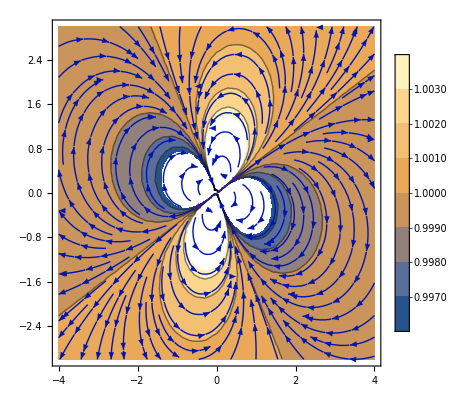

```mathematica
{{xMin,xMax},{yMin,yMax}}={{-4,4},{-3,3}};
ϵ=0.001;
f[z_]:= (1.2+ⅈ)+(3.2 -2 ⅈ)(1/(z+ϵ ⅈ)-1/(z-ϵ ⅈ))
vel[{x_,y_}]:=ReIm[f'[x+ⅈ y]]*{1,-1}
Show[
ContourPlot[Im[f[x+ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic],
StreamPlot[vel[{x,y}],{x,xMin,xMax},{y,yMin,yMax}]
]
```

```mathematica
{{xMin,xMax},{yMin,yMax}}={{-4,4},{-3,3}};
ϵ=0.001;
f[z_]:= (1.2+ⅈ)+(3.2 -2 ⅈ)(1/(z+ϵ ⅈ)-1/(z-ϵ ⅈ))
vel[{x_,y_}]:=ReIm[f'[x+ⅈ y]]*{1,-1}
Show[
ContourPlot[Im[f[x+ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic],
StreamPlot[vel[{x,y}],{x,xMin,xMax},{y,yMin,yMax}]
]
```

## Joukowski Airfoil

The conformal mapping
	z→z+1/z
does nice things to the inside and outside of the unit circle!

### First a rectangle.

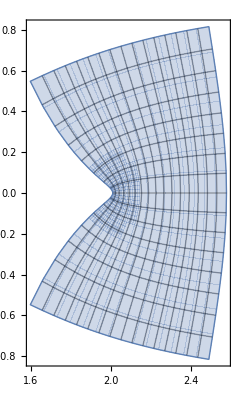

```mathematica
f[z_]:=z+1/z
{{xMin,xMax},{yMin,yMax}}={{1.1,2.1},{-1,1}};
ParametricPlot[ReIm[f[x+ ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},Mesh->Automatic]
```

### The outside of the unit circle.

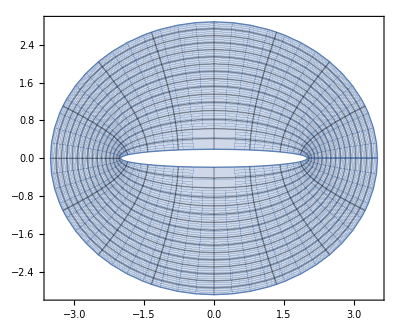

```mathematica
f[z_]:=z+1/z
{{rMin,rMax},{θMin,θMax}}={{1.1,3.2},{0,2π}};
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,rMin,rMax},{θ,θMin,θMax},Mesh->Automatic]
```

### The inside of the unit circle.

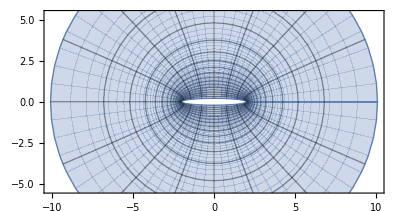

```mathematica
f[z_]:=z+1/z
{{rMin,rMax},{θMin,θMax}}={{0.1,0.9},{0,2π}};
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,rMin,rMax},{θ,θMin,θMax},Mesh->Automatic]
```

### The Joukowski airfoil

Apparently the image of any circle passing through z_1=1 and enclosing z_2=-1 is mapped onto something that looks like an airfoil!  The center of the circle is a single complex parameter.  The radius r is the distance to z=1. Of course, to be useful the radius needs to be large enough to enclose the non-conformal point at z=-1 in the mapping z+1/z at z=-1

```mathematica
Manipulate[
zc=c.{1,ⅈ};
r=Abs[zc-1];
ParametricPlot[
{ReIm[zc+r ⅇ^(ⅈ θ)],ReIm[f[zc+r ⅇ^(ⅈ θ)]]},
{θ,0, 2π},PlotRange->{{-10,3},{-7,7}},Epilog->{Point[{1,0}],Point[{-1,0}]}],
{{c,{-1,1}},Locator}]
```

are one complex parameter c The center of a circle through z_1 and z_2 is 
	center =0+ⅈ c 
for some c because it lies on the perpendicular to the bisector. Our three equations for the circle through a third point x+ⅈ y are 
	1 | + | c^2 | = | r^2
(-1)^2 | + | c^2 | = | r^2
x^2 | + | (c-y)^2 | = | r^2
Solving the first two gives 
	r^2=c^2+1
and plugging into the last equation gives
	x^2 | + | (c-y)^2 | = | c^2+1
Expanding and canceling the c^2 on both sides gives 
	(x^2+y^2)-2 c y =1
which gives (provided y≠0
	c=(x^2+y^2-1)/(2 y) and of course r=√(c^2+1).

```mathematica
Manipulate[
{x,y}=p;
c=(x^2+y^2-1)/(2 y); r=√(c^2+1);
Graphics[{PointSize[0.02],
{Green, Line[{{-1,0},{1,0}}]},
{Purple,Circle[{0,c},r]},
{Red,Point[{-1,0}]},
{Blue,Point[{1,0}]},
Line[{{0,0},p}]},
PlotRange->2,Axes->Automatic],{{p,{1,1}},Locator}]
```

Finally lets see the airfoils

```mathematica
f[z_]:=z + 1/z
Manipulate[
c=(x^2+y^2-1)/(2 y); r=√(c^2+1);
ParametricPlot[{
ReIm[f[c ⅈ+r ⅇ^(ⅈ θ)]],
ReIm[c ⅈ+r ⅇ^(ⅈ θ)]},{θ,0, 4π},
PlotRange->{{-5,5},{-5,5}},
Epilog->{Purple, Point[{x,y}]}],
{{x,0.2},-2,2},{{y,-0.3},-2,2}]
```

```mathematica
{x3,y3}={1.2,2.3}
```

{1.2,2.3}

```mathematica
Manipulate[
{x,y}=p;
c=(x^2+y^2-1)/(2 y); r=√(c^2+1);
Graphics[{PointSize[0.02],
{Green, Line[{{-1,0},{1,0}}]},
{Purple,Circle[{0,c},r]},
{Red,Point[{-1,0}]},
{Blue,Point[{1,0}]},
Line[{{0,0},p}]},
PlotRange->2,Axes->Automatic],{{p,{1,1}},Locator
```